# Mean Field solution - seaming two Kitaev materials

```mathematica
Needs["MaTeX`"]
```

```mathematica
Dynamic[Refresh[NotebookSave[];DateString[],UpdateInterval->60]]
```

### Definitions [Run this!]

the Hamiltonian

```mathematica
r[J_]=J;
s[k_,J_]=-2J Cos[k/2];
α[k_,κ_] = 2 κ Sin [k];
β[k_,κ_] =  2 κ Sin [k/2];
γ[h_] = -h;
```

```mathematica
HZMF[k_,n_, J_,κ_,h_,Jt_,χc_,χb_] := SparseArray[   {
					{i_,i_} -> If[ 1<i<2n+ 4 , If[OddQ[i],-α[k,κ], α[k,κ]] , 0],

					{i_,j_} /;Abs[i-j]==1->   
												If[                     ((i==1)∨(j==1))∨((i==2n+ 4)∨(j==2n+ 4)), 
															If[ ((i==1)∨(i==2n+4)), ⅈ γ[h] , - ⅈ γ[h] ], 
															If[EvenQ[Min[i,j]], -(i-j) ⅈ s[k,J] , -(i-j) ⅈ r[J]] ],

					{i_,j_} /;Abs[i-j]==2-> If[ ((i==1)∨(j==1))∨((i==2n+ 4)∨(j==2n+ 4)), 0,  If[OddQ[i],β[k,κ], -β[k,κ]] ],
					  {1,2n+ 4}->  ⅈ Jt χc ,
						{2,2n+ 3} ->  ⅈ Jt χb,
						{2n+ 4,1} -> - ⅈ Jt χc ,
						{2n+ 3,2} -> - ⅈ Jt χb
},					
	{2n+ 4,2n+ 4}					]
```

the sorting [ first positive and the negative energies ]

```mathematica
MySort[list_] :=If[         EvenQ@Length[list],
					Flatten[{Drop[SortBy[list,First],Length[list]/2],Reverse@Take[SortBy[list,First],Length[list]/2]},1]
                                               ,0];
```

#### values for the mean-fields

```mathematica
cSol= {{0.,-5.998669191660753*^-14},{0.01,-0.000023146144462346553},{0.02,-0.00004751835988648067},{0.03,-0.00007408254526323681},{0.04,-0.00010394098460126548},{0.05,-0.0001384975353043768},{0.060000000000000005,-0.00017956031877135257},{0.07,-0.00022972257830976885},{0.08,-0.00029065577230992973},{0.09,-0.00036927045034124427},{0.09999999999999999,-0.0004731922345432506},{0.10999999999999999,-0.0006033084858643212},{0.11999999999999998,-0.0007932404360109966},{0.12999999999999998,-0.0010426518794959408},{0.13999999999999999,-0.0014049144970563919},{0.15,-0.0019842180343151677},{0.16,-0.0028039942228650842},{0.17,-0.004064802363130176},{0.18000000000000002,-0.005806926682324859},{0.19000000000000003,-0.008091939662849346},{0.20000000000000004,-0.010950719675347076},{0.21000000000000005,-0.014374505908245684},{0.22000000000000006,-0.018404155511166177},{0.23000000000000007,-0.022823890652217495},{0.24000000000000007,-0.02765849821987271},{0.25000000000000006,-0.03290582045555088},{0.26000000000000006,-0.03836734311724329},{0.2700000000000001,-0.04407062483334689},{0.2800000000000001,-0.050029017752459444},{0.2900000000000001,-0.05607818832222443},{0.3000000000000001,-0.06225886832196042},{0.3100000000000001,-0.06854581846055087},{0.3200000000000001,-0.07493961823474803},{0.3300000000000001,-0.08140378784164332},{0.34000000000000014,-0.08789081169409377},{0.35000000000000014,-0.09442086573038835},{0.36000000000000015,-0.10098341193220588},{0.37000000000000016,-0.10756930919037823},{0.38000000000000017,-0.11417050389513685},{0.3900000000000002,-0.12077979914715131},{0.4000000000000002,-0.12740481559467198},{0.4100000000000002,-0.13400942768591853},{0.4200000000000002,-0.14060440534978566},{0.4300000000000002,-0.14718458234521967},{0.4400000000000002,-0.1537451350552678},{0.45000000000000023,-0.1602815343480911},{0.46000000000000024,-0.1668011199774982},{0.47000000000000025,-0.17327551283367065},{0.48000000000000026,-0.1797140478972435},{0.49000000000000027,-0.18611326834169512},{0.5000000000000002,-0.19246991156815907},{0.5100000000000002,-0.19878116434716556},{0.5200000000000002,-0.20504424937318436},{0.5300000000000002,-0.2112567115500048},{0.5400000000000003,-0.2174163356400951},{0.5500000000000003,-0.22352112982182995},{0.5600000000000003,-0.2295693639268497},{0.5700000000000003,-0.23555949054553588},{0.5800000000000003,-0.24149018640784062},{0.5900000000000003,-0.2473603294633414},{0.6000000000000003,-0.253168988644746},{0.6100000000000003,-0.25891991884828364},{0.6200000000000003,-0.26460308859895987},{0.6300000000000003,-0.2702230620637436},{0.6400000000000003,-0.27577955761689543},{0.6500000000000004,-0.2812724287996291},{0.6600000000000004,-0.28670165575608936},{0.6700000000000004,-0.29206733078367747},{0.6800000000000004,-0.2973696407484801},{0.6900000000000004,-0.3026088964359929},{0.7000000000000004,-0.30778546068027307},{0.7100000000000004,-0.312899782973236},{0.7200000000000004,-0.3179523795891915},{0.7300000000000004,-0.32294382570916697},{0.7400000000000004,-0.3278747480884418},{0.7500000000000004,-0.33274581958431887},{0.7600000000000005,-0.3375577471081537},{0.7700000000000005,-0.3423112753575533},{0.7800000000000005,-0.34700717453294955},{0.7900000000000005,-0.3516462374853931},{0.8000000000000005,-0.3562292753296379},{0.8100000000000005,-0.36075711346999195},{0.8200000000000005,-0.36523058934867064},{0.8300000000000005,-0.36965054390060753},{0.8400000000000005,-0.3743028021927961},{0.8500000000000005,-0.37860097346347865},{0.8600000000000005,-0.38284933691212125},{0.8700000000000006,-0.387048656047403},{0.8800000000000006,-0.39119969650577674},{0.8900000000000006,-0.3953032240088378},{0.9000000000000006,-0.39936000254896686},{0.9100000000000006,-0.4033707927840085},{0.9200000000000006,-0.40733635062291856},{0.9300000000000006,-0.41125742598547893},{0.9400000000000006,-0.4151347617203428},{0.9500000000000006,-0.4189690926667919},{0.9600000000000006,-0.42276114484667743},{0.9700000000000006,-0.42651163477404924},{0.9800000000000006,-0.430221268870989},{0.9900000000000007,-0.43389074297907615},{1.0000000000000007,-0.43752074195680457},{1.0100000000000007,-0.4411119393541041},{1.0200000000000007,-0.4446649971558698},{1.0300000000000007,-0.4481805655871278}} ;
```

```mathematica
bSol={{0.,-4.162971305723012*^-14},{0.01,0.004647831884441789},{0.02,0.004710839988859343},{0.03,0.004809737892123496},{0.04,0.004952437664483306},{0.05,0.005150808219058515},{0.060000000000000005,0.005421847962868142},{0.07,0.005791246345170904},{0.08,0.00628037567091825},{0.09,0.006958140329115015},{0.09999999999999999,0.007907174083053848},{0.10999999999999999,0.009157286776586891},{0.11999999999999998,0.011044702445576147},{0.12999999999999998,0.013600390634332582},{0.13999999999999999,0.01735122075475491},{0.15,0.02327367167909811},{0.16,0.031404061322200846},{0.17,0.04328119704703344},{0.18000000000000002,0.05877252298407581},{0.19000000000000003,0.07787992978693209},{0.20000000000000004,0.10028655866090619},{0.21000000000000005,0.12537914426727273},{0.22000000000000006,0.15293484395675325},{0.23000000000000007,0.18111934406299438},{0.24000000000000007,0.20987326584453417},{0.25000000000000006,0.2389725439843777},{0.26000000000000006,0.26721812267343015},{0.2700000000000001,0.2947603723890427},{0.2800000000000001,0.3216516845705917},{0.2900000000000001,0.3471804809377423},{0.3000000000000001,0.3716182050368079},{0.3100000000000001,0.3949394391745629},{0.3200000000000001,0.4172277608464468},{0.3300000000000001,0.4384255283843356},{0.34000000000000014,0.4584709853436415},{0.35000000000000014,0.47752315785760213},{0.36000000000000015,0.4956314564180262},{0.37000000000000016,0.5128469778698983},{0.38000000000000017,0.5292206714627025},{0.3900000000000002,0.5448021582900172},{0.4000000000000002,0.559673459369176},{0.4100000000000002,0.5738048361435444},{0.4200000000000002,0.5872800637275449},{0.4300000000000002,0.600138567363744},{0.4400000000000002,0.612417112369845},{0.45000000000000023,0.6241498713970991},{0.46000000000000024,0.6353907496684346},{0.47000000000000025,0.6461218533331807},{0.48000000000000026,0.6563963490877621},{0.49000000000000027,0.6662395932360523},{0.5000000000000002,0.6756750620191384},{0.5100000000000002,0.6847249342866867},{0.5200000000000002,0.6934095322117786},{0.5300000000000002,0.7017479439620438},{0.5400000000000003,0.7097580044817575},{0.5500000000000003,0.7174563844645572},{0.5600000000000003,0.7248587503984847},{0.5700000000000003,0.731979745523456},{0.5800000000000003,0.7388331404363013},{0.5900000000000003,0.7454318821246291},{0.6000000000000003,0.7517881559967322},{0.6100000000000003,0.757919075814085},{0.6200000000000003,0.763823537427677},{0.6300000000000003,0.7695181319994803},{0.6400000000000003,0.7750124958919181},{0.6500000000000004,0.7803157358151543},{0.6600000000000004,0.7854364659804596},{0.6700000000000004,0.7903828352384747},{0.6800000000000004,0.7951625483772904},{0.6900000000000004,0.7997829353917575},{0.7000000000000004,0.8042509080696512},{0.7100000000000004,0.8085730305821881},{0.7200000000000004,0.8127555280917151},{0.7300000000000004,0.8168043065392177},{0.7400000000000004,0.8207249711115414},{0.7500000000000004,0.8245228447730737},{0.7600000000000005,0.8282029788781645},{0.7700000000000005,0.8317701774672912},{0.7800000000000005,0.8352290046990077},{0.7900000000000005,0.8385838001023542},{0.8000000000000005,0.8418386911019167},{0.8100000000000005,0.8449976047923273},{0.8200000000000005,0.8480642801655964},{0.8300000000000005,0.851042273920805},{0.8400000000000005,0.8541779538407985},{0.8500000000000005,0.856971010382526},{0.8600000000000005,0.8596865081811447},{0.8700000000000006,0.8623272577608911},{0.8800000000000006,0.8648959462704625},{0.8900000000000006,0.8673951435498269},{0.9000000000000006,0.8698273078956804},{0.9100000000000006,0.8721947915381045},{0.9200000000000006,0.8744998458407897},{0.9300000000000006,0.8767446262369714},{0.9400000000000006,0.8789311969129804},{0.9500000000000006,0.8810615352510495},{0.9600000000000006,0.8831375360427073},{0.9700000000000006,0.8851610154837977},{0.9800000000000006,0.8871337149618},{0.9900000000000007,0.8890573046457928},{1.0000000000000007,0.8909333868890305},{1.0100000000000007,0.8927634994537234},{1.0200000000000007,0.894549118567233},{1.0300000000000007,0.8962916618185405}};
```

/the Transpose does not work for unite this type of list, denote by bc the list of elements of the type { jt , χc , χb }

```mathematica
bc = {};
For[ i=1,i  <  Length[cSol] , i = i+1 ,  AppendTo[bc, { cSol[[i]][[1]],cSol[[i]][[2]],bSol[[i]][[2]] }] ]
```

### Self consistent solution

```mathematica
n=250-2;
J=1;
{hx,hy,hz}=0.85/√3{1,1,1};
κ = hx*hy*hz;
(*Jt=0;*)
Lx=500;
steps=20;
deltaJt=0.02;
acuracy = 3;
```

I will allocate the  points { J̃, χ } in matrix “b” and “c”, for this I initialize two empty matrices and at the end of each loop  I append output of each loop to the matrix.

#### code

```mathematica
t0 = AbsoluteTime[];
b = {};
c = {};
j0 =0.0;
jf  =0.4;
For[jt=j0,jt<jf,jt=jt+deltaJt,
	chib = Table[0,steps];
	chib⟦1⟧= If[jt==j0,0,0.005+ 1.02b⟦Round[(jt-j0)/deltaJt]⟧⟦2⟧ ];
	chic = Table[0,steps];
	chic⟦1⟧ =   If[jt==j0,0, -0.001+ 1.02 c⟦Round[(jt-j0)/deltaJt]⟧⟦2⟧ ];
	Δa=1;
	Δb=1;
	(*Δc=1;*)
	For[i=1,(( i<steps)∧( (Δa≠ 0)∨(Δb≠0)) )  , i++,												
		EV =  Table[  {k, Transpose[Chop@MySort@Transpose@Quiet@Eigensystem[N@HZMF[k,n, J,κ,hz,jt,chic⟦i⟧,chib⟦i⟧ ] ]]⟦2⟧   } , {k,0,π , π/Lx}];
							chic⟦i+1⟧=2/Lx Sum[  Sum[  Im[Conjugate[EV⟦k⟧⟦2⟧⟦m⟧⟦2⟧]*EV⟦k⟧⟦2⟧⟦m⟧⟦2n+3⟧
						] , {m,1,n+2}]  , {k,1,Lx}] ;
							chib⟦i+1⟧=2/Lx Sum[  Sum[ Im[Conjugate[EV⟦k⟧⟦2⟧⟦m⟧⟦1⟧]*EV⟦k⟧⟦2⟧⟦m⟧⟦2n+4⟧  ] , {m,1,n+2}]
						 , {k,1,Lx}]  ;
(* Print[chic[[i+1]] "c="];*)
Δa = Chop[Abs[Abs@chib⟦i+1⟧-Abs@ chib⟦i⟧ ], 10^-acuracy]+Chop[Abs[ Abs@chic⟦i+1⟧-Abs@ chic⟦i⟧ ], 10^-acuracy ];
Δb = If[i==1,1.0 ,Chop[Abs[Abs@chib⟦i⟧-Abs@ chib⟦i-1⟧ ], 10^-acuracy]+Chop[Abs[ Abs@chic⟦i⟧-Abs@ chic⟦i-1⟧ ], 10^-acuracy ]]
(*Δc = If[i≤ 2,1.0 ,Chop[Abs[Abs@chib⟦i-1⟧-Abs@ chib⟦i-2⟧ ], 10^-acuracy]+Chop[Abs[ Abs@chic⟦i-1⟧-Abs@ chic⟦i-2⟧ ], 10^-acuracy ]];*)
(*Print[Δa"deltaA="];
Print[Δc"deltaC="];*)
		];(*Print["χb="Last[chib]]; Print["χc="Last[chic]];*)
	(*t=AbsoluteTime[];*)
	(*Print["Jt = ",jt , ";  Max Step: i=",i , ";  Timing = ",  Floor[(t-t0)/3600], "h ",Floor[(t-t0)/60-60*Floor[(t-t0)/3600]], "m"];*)
	AppendTo[ b , {jt , chib⟦i⟧ } ];
	 AppendTo[ c , {jt ,chic⟦i⟧} ] 
 ]
```

$Aborted

```mathematica
c
```

```mathematica
b
```

#### Plot

```mathematica
lineJt = Line[ {{0.13,-1.5},{0.13,2.0}}];
```

```mathematica
bPlot = ListPlot[ b, FrameLabel-> { MaTeX["\\tilde{J}",Magnification->2] ,  MaTeX["\\chi_b",Magnification->2] } , PlotRange-> {0,1},Joined->False, PlotMarkers->{"●"},Frame->True,PlotStyle->{Darker[Blue]},   FrameStyle->Directive[Black,16],ImageSize->500 ,  PlotLabel-> Style[MaTeX["\\ell_x=\\ell_y=500",Magnification->1.8] ,20 ,Black ] (*, Epilog-> {Directive[Thin,Black,Dashed],lineJt}*)]
```

-Graphics-

```mathematica
cPlot=ListPlot[ c, FrameLabel-> { MaTeX["\\tilde{J}",Magnification->2] ,  MaTeX["\\chi_c",Magnification->2] }  ,   PlotRange-> {-1.5/2,0},Joined->False,PlotMarkers->{"●"},Frame->True,PlotStyle->{Darker[Red]}, Frame->True,  FrameStyle->Directive[Black,16],ImageSize->500 ,  PlotLabel-> Style[MaTeX["\\ell_x=\\ell_y=500",Magnification->1.8] ,20 ,Black ] (*,Epilog-> {Directive[Thin,Black,Dashed],lineJt}*)]
```

-Graphics-

### Self consistent solution

```mathematica
n=100-2;
J=1;
{hx,hy,hz}=0.85/√3{1,1,1};
κ = hx*hy*hz;
(*Jt=0;*)
Lx=200;
steps=20;
deltaJt=0.02;
acuracy = 3;
```

I will allocate the  points { J̃, χ } in matrix “b” and “c”, for this I initialize two empty matrices and at the end of each loop  I append output of each loop to the matrix.

#### code

```mathematica
(*t0 = AbsoluteTime[];*)
b = {};
c = {};
j0 =0.0;
jf  =0.5;
For[jt=j0,jt<jf,jt=jt+deltaJt,
	chib = Table[0,steps];
	chib⟦1⟧= If[jt==j0,0,0.005+ 1.02b⟦Round[(jt-j0)/deltaJt]⟧⟦2⟧ ];
	chic = Table[0,steps];
	chic⟦1⟧ =   If[jt==j0,0, -0.001+ 1.02 c⟦Round[(jt-j0)/deltaJt]⟧⟦2⟧ ];
	Δa=1;
	Δb=1;
	(*Δc=1;*)
	For[i=1,(( i<steps)∧( (Δa≠ 0)∨(Δb≠0)) )  , i++,												
		EV =  Table[  {k, Transpose[Chop@MySort@Transpose@Quiet@Eigensystem[N@HZMF[k,n, J,κ,hz,jt,chic⟦i⟧,chib⟦i⟧ ] ]]⟦2⟧   } , {k,0,π , π/Lx}];
							chic⟦i+1⟧=2/Lx Sum[  Sum[  Im[Conjugate[EV⟦k⟧⟦2⟧⟦m⟧⟦2⟧]*EV⟦k⟧⟦2⟧⟦m⟧⟦2n+3⟧
						] , {m,1,n+2}]  , {k,1,Lx}] ;
							chib⟦i+1⟧=2/Lx Sum[  Sum[ Im[Conjugate[EV⟦k⟧⟦2⟧⟦m⟧⟦1⟧]*EV⟦k⟧⟦2⟧⟦m⟧⟦2n+4⟧  ] , {m,1,n+2}]
						 , {k,1,Lx}]  ;
(* Print[chic[[i+1]] "c="];*)
Δa = Chop[Abs[Abs@chib⟦i+1⟧-Abs@ chib⟦i⟧ ], 10^-acuracy]+Chop[Abs[ Abs@chic⟦i+1⟧-Abs@ chic⟦i⟧ ], 10^-acuracy ];
Δb = If[i==1,1.0 ,Chop[Abs[Abs@chib⟦i⟧-Abs@ chib⟦i-1⟧ ], 10^-acuracy]+Chop[Abs[ Abs@chic⟦i⟧-Abs@ chic⟦i-1⟧ ], 10^-acuracy ]]
(*Δc = If[i≤ 2,1.0 ,Chop[Abs[Abs@chib⟦i-1⟧-Abs@ chib⟦i-2⟧ ], 10^-acuracy]+Chop[Abs[ Abs@chic⟦i-1⟧-Abs@ chic⟦i-2⟧ ], 10^-acuracy ]];*)
(*Print[Δa"deltaA="];
Print[Δc"deltaC="];*)
		];(*Print["χb="Last[chib]]; Print["χc="Last[chic]];*)
	(*t=AbsoluteTime[];*)
	(*Print["Jt = ",jt , ";  Max Step: i=",i , ";  Timing = ",  Floor[(t-t0)/3600], "h ",Floor[(t-t0)/60-60*Floor[(t-t0)/3600]], "m"];*)
	AppendTo[ b , {jt , chib⟦i⟧ } ];
	 AppendTo[ c , {jt ,chic⟦i⟧} ] 
 ]
```

$Aborted

```mathematica
c
b
```

#### Plot

```mathematica
lineJt = Line[ {{0.08,-1.5},{0.08,2.0}}];
```

```mathematica
bPlot = ListPlot[ b, FrameLabel-> { MaTeX["\\tilde{J}",Magnification->2] ,  MaTeX["\\chi_b",Magnification->2] } , PlotRange-> {0,1},Joined->False, PlotMarkers->{"●"},Frame->True,PlotStyle->{Darker[Blue]},   FrameStyle->Directive[Black,16],ImageSize->500 ,  PlotLabel-> Style[MaTeX["\\ell_x=\\ell_y=200",Magnification->1.8] ,20 ,Black ] (*, Epilog-> {Directive[Thin,Black,Dashed],lineJt}*)]
```

```mathematica
cPlot=ListPlot[ c, FrameLabel-> { MaTeX["\\tilde{J}",Magnification->2] ,  MaTeX["\\chi_c",Magnification->2] }  ,   PlotRange-> {-1.5/2,0},Joined->False,PlotMarkers->{"●"},Frame->True,PlotStyle->{Darker[Red]}, Frame->True,  FrameStyle->Directive[Black,16],ImageSize->500 ,  PlotLabel-> Style[MaTeX["\\ell_x=\\ell_y=200",Magnification->1.8] ,20 ,Black ] (*, Epilog-> {Directive[Thin,Black,Dashed],lineJt}*)]
```

### Self consistent solution

```mathematica
n=150-2;
J=1;
{hx,hy,hz}=0.85/√3{1,1,1};
κ = hx*hy*hz;
(*Jt=0;*)
Lx=300;
steps=20;
deltaJt=0.02;
acuracy = 3;
```

I will allocate the  points { J̃, χ } in matrix “b” and “c”, for this I initialize two empty matrices and at the end of each loop  I append output of each loop to the matrix.

#### code

```mathematica
(*t0 = AbsoluteTime[];*)
b = {};
c = {};
j0 =0.0;
jf  =0.5;
For[jt=j0,jt<jf,jt=jt+deltaJt,
	chib = Table[0,steps];
	chib⟦1⟧= If[jt==j0,0,0.005+ 1.02b⟦Round[(jt-j0)/deltaJt]⟧⟦2⟧ ];
	chic = Table[0,steps];
	chic⟦1⟧ =   If[jt==j0,0, -0.001+ 1.02 c⟦Round[(jt-j0)/deltaJt]⟧⟦2⟧ ];
	Δa=1;
	Δb=1;
	(*Δc=1;*)
	For[i=1,(( i<steps)∧( (Δa≠ 0)∨(Δb≠0)) )  , i++,												
		EV =  Table[  {k, Transpose[Chop@MySort@Transpose@Quiet@Eigensystem[N@HZMF[k,n, J,κ,hz,jt,chic⟦i⟧,chib⟦i⟧ ] ]]⟦2⟧   } , {k,0,π , π/Lx}];
							chic⟦i+1⟧=2/Lx Sum[  Sum[  Im[Conjugate[EV⟦k⟧⟦2⟧⟦m⟧⟦2⟧]*EV⟦k⟧⟦2⟧⟦m⟧⟦2n+3⟧
						] , {m,1,n+2}]  , {k,1,Lx}] ;
							chib⟦i+1⟧=2/Lx Sum[  Sum[ Im[Conjugate[EV⟦k⟧⟦2⟧⟦m⟧⟦1⟧]*EV⟦k⟧⟦2⟧⟦m⟧⟦2n+4⟧  ] , {m,1,n+2}]
						 , {k,1,Lx}]  ;
(* Print[chic[[i+1]] "c="];*)
Δa = Chop[Abs[Abs@chib⟦i+1⟧-Abs@ chib⟦i⟧ ], 10^-acuracy]+Chop[Abs[ Abs@chic⟦i+1⟧-Abs@ chic⟦i⟧ ], 10^-acuracy ];
Δb = If[i==1,1.0 ,Chop[Abs[Abs@chib⟦i⟧-Abs@ chib⟦i-1⟧ ], 10^-acuracy]+Chop[Abs[ Abs@chic⟦i⟧-Abs@ chic⟦i-1⟧ ], 10^-acuracy ]]
(*Δc = If[i≤ 2,1.0 ,Chop[Abs[Abs@chib⟦i-1⟧-Abs@ chib⟦i-2⟧ ], 10^-acuracy]+Chop[Abs[ Abs@chic⟦i-1⟧-Abs@ chic⟦i-2⟧ ], 10^-acuracy ]];*)
(*Print[Δa"deltaA="];
Print[Δc"deltaC="];*)
		];(*Print["χb="Last[chib]]; Print["χc="Last[chic]];*)
	(*t=AbsoluteTime[];*)
	(*Print["Jt = ",jt , ";  Max Step: i=",i , ";  Timing = ",  Floor[(t-t0)/3600], "h ",Floor[(t-t0)/60-60*Floor[(t-t0)/3600]], "m"];*)
	AppendTo[ b , {jt , chib⟦i⟧ } ];
	 AppendTo[ c , {jt ,chic⟦i⟧} ] 
 ]
```

```mathematica
c
b
```

#### Plot

```mathematica
lineJt = Line[ {{0.08,-1.5},{0.08,2.0}}];
```

```mathematica
bPlot = ListPlot[ b, FrameLabel-> { MaTeX["\\tilde{J}",Magnification->2] ,  MaTeX["\\chi_b",Magnification->2] } , PlotRange-> {0,1},Joined->False, PlotMarkers->{"●"},Frame->True,PlotStyle->{Darker[Blue]},   FrameStyle->Directive[Black,16],ImageSize->500 ,  PlotLabel-> Style[MaTeX["\\ell_x=\\ell_y=300",Magnification->1.8] ,20 ,Black ] (*, Epilog-> {Directive[Thin,Black,Dashed],lineJt}*)]
```

```mathematica
cPlot=ListPlot[ c, FrameLabel-> { MaTeX["\\tilde{J}",Magnification->2] ,  MaTeX["\\chi_c",Magnification->2] }  ,   PlotRange-> {-1.5/2,0},Joined->False,PlotMarkers->{"●"},Frame->True,PlotStyle->{Darker[Red]}, Frame->True,  FrameStyle->Directive[Black,16],ImageSize->500 ,  PlotLabel-> Style[MaTeX["\\ell_x=\\ell_y=300",Magnification->1.8] ,20 ,Black ] (*, Epilog-> {Directive[Thin,Black,Dashed],lineJt}*)]
```

### Self consistent solution

```mathematica
n=200-2;
J=1;
{hx,hy,hz}=0.85/√3{1,1,1};
κ = hx*hy*hz;
(*Jt=0;*)
Lx=400;
steps=20;
deltaJt=0.02;
acuracy = 3;
```

I will allocate the  points { J̃, χ } in matrix “b” and “c”, for this I initialize two empty matrices and at the end of each loop  I append output of each loop to the matrix.

#### code

```mathematica
(*t0 = AbsoluteTime[];*)
b = {};
c = {};
j0 =0.0;
jf  =0.5;
For[jt=j0,jt<jf,jt=jt+deltaJt,
	chib = Table[0,steps];
	chib⟦1⟧= If[jt==j0,0,0.005+ 1.02b⟦Round[(jt-j0)/deltaJt]⟧⟦2⟧ ];
	chic = Table[0,steps];
	chic⟦1⟧ =   If[jt==j0,0, -0.001+ 1.02 c⟦Round[(jt-j0)/deltaJt]⟧⟦2⟧ ];
	Δa=1;
	Δb=1;
	(*Δc=1;*)
	For[i=1,(( i<steps)∧( (Δa≠ 0)∨(Δb≠0)) )  , i++,												
		EV =  Table[  {k, Transpose[Chop@MySort@Transpose@Quiet@Eigensystem[N@HZMF[k,n, J,κ,hz,jt,chic⟦i⟧,chib⟦i⟧ ] ]]⟦2⟧   } , {k,0,π , π/Lx}];
							chic⟦i+1⟧=2/Lx Sum[  Sum[  Im[Conjugate[EV⟦k⟧⟦2⟧⟦m⟧⟦2⟧]*EV⟦k⟧⟦2⟧⟦m⟧⟦2n+3⟧
						] , {m,1,n+2}]  , {k,1,Lx}] ;
							chib⟦i+1⟧=2/Lx Sum[  Sum[ Im[Conjugate[EV⟦k⟧⟦2⟧⟦m⟧⟦1⟧]*EV⟦k⟧⟦2⟧⟦m⟧⟦2n+4⟧  ] , {m,1,n+2}]
						 , {k,1,Lx}]  ;
(* Print[chic[[i+1]] "c="];*)
Δa = Chop[Abs[Abs@chib⟦i+1⟧-Abs@ chib⟦i⟧ ], 10^-acuracy]+Chop[Abs[ Abs@chic⟦i+1⟧-Abs@ chic⟦i⟧ ], 10^-acuracy ];
Δb = If[i==1,1.0 ,Chop[Abs[Abs@chib⟦i⟧-Abs@ chib⟦i-1⟧ ], 10^-acuracy]+Chop[Abs[ Abs@chic⟦i⟧-Abs@ chic⟦i-1⟧ ], 10^-acuracy ]]
(*Δc = If[i≤ 2,1.0 ,Chop[Abs[Abs@chib⟦i-1⟧-Abs@ chib⟦i-2⟧ ], 10^-acuracy]+Chop[Abs[ Abs@chic⟦i-1⟧-Abs@ chic⟦i-2⟧ ], 10^-acuracy ]];*)
(*Print[Δa"deltaA="];
Print[Δc"deltaC="];*)
		];(*Print["χb="Last[chib]]; Print["χc="Last[chic]];*)
	(*t=AbsoluteTime[];*)
	(*Print["Jt = ",jt , ";  Max Step: i=",i , ";  Timing = ",  Floor[(t-t0)/3600], "h ",Floor[(t-t0)/60-60*Floor[(t-t0)/3600]], "m"];*)
	AppendTo[ b , {jt , chib⟦i⟧ } ];
	 AppendTo[ c , {jt ,chic⟦i⟧} ] 
 ]
```

```mathematica
c
b
```

#### Plot

```mathematica
lineJt = Line[ {{0.08,-1.5},{0.08,2.0}}];
```

```mathematica
bPlot = ListPlot[ b, FrameLabel-> { MaTeX["\\tilde{J}",Magnification->2] ,  MaTeX["\\chi_b",Magnification->2] } , PlotRange-> {0,1},Joined->False, PlotMarkers->{"●"},Frame->True,PlotStyle->{Darker[Blue]},   FrameStyle->Directive[Black,16],ImageSize->500 ,  PlotLabel-> Style[MaTeX["\\ell_x=\\ell_y=400",Magnification->1.8] ,20 ,Black ] (*, Epilog-> {Directive[Thin,Black,Dashed],lineJt}*)]
```

```mathematica
cPlot=ListPlot[ c, FrameLabel-> { MaTeX["\\tilde{J}",Magnification->2] ,  MaTeX["\\chi_c",Magnification->2] }  ,   PlotRange-> {-1.5/2,0},Joined->False,PlotMarkers->{"●"},Frame->True,PlotStyle->{Darker[Red]}, Frame->True,  FrameStyle->Directive[Black,16],ImageSize->500 ,  PlotLabel-> Style[MaTeX["\\ell_x=\\ell_y=400",Magnification->1.8] ,20 ,Black ] (*, Epilog-> {Directive[Thin,Black,Dashed],lineJt}*)]
```

### Phase diagram

### Dispersion in each phase

```mathematica
Energies[n_,J_,κ_ ,h_, P_,Jt_,χc_,χb_] :=  Table[  N@ {   k, Chop@Sort[Eigenvalues[ N@ HZMF[k, n, J,κ,h ,Jt,χc,χb ]  ]]    }     , {k,0,2π , 2π/(P-1)}]
```

```mathematica
n = 100;
P = 100;
J = 1;
```

```mathematica
dispersion[E_,P_,n_]:= Transpose[    Table[  { E⟦i⟧⟦1⟧ , E⟦i⟧⟦2⟧⟦j⟧} , {i,1,P} , {j,1,2*n+4}]  ]
```

```mathematica
edge[D_,n_] := D⟦ {n+1,n+2,n+3,n+4} ⟧
bulk[D_,n_] := D⟦ {1,n,n+5,2n+4} ⟧
```

#### For J tilde smaller than the critical J

```mathematica
{hx,hy,hz}=N[ 0.85{1,1,1}/Sqrt[3]];
```

```mathematica
Timing[eGapless = Energies[n,1,hx hy hz,hz, P,  0.07 ,-0.00022972257830976885 , 0.005791246345170904]]⟦1⟧/60 //Quiet
```

0.0541667

```mathematica
dGapless = dispersion[eGapless,P,n];
```

```mathematica
(*ListPlot[ dGapless , Joined->True ,  PlotRange-> All , FrameLabel->{MaTeX["q",Magnification->2] , MaTeX["\\epsilon",Magnification->2] }  ,  PlotLabel-> Style[MaTeX["\\text{Dispersion for } \\mathbf{h} = 0.85 \\, \\mathbf{c} \\text{ and } \\tilde{J} = 0.07 J ",Magnification->2] ,20 ,Black ] ,
PlotStyle->  {{Black,Thickness[0.004]},{Black,Thickness[0.004]},{Black,Thickness[0.004]},{Black,Thickness[0.004]}},   FrameTicks->{{-π,-2π/3  , -π/3 ,0,π/3 , 2π/3  , π, 4π/3 , 5π/3  , 2π} , Automatic}   ,Joined->True,   Frame->{{True,False} ,{True,False}} , FrameStyle ->Directive[Black,26], FrameTicksStyle->Directive[Black,15],ImageSize->800]*)
```

```mathematica
edGapless= edge[ dGapless,n];
bulkGapless = bulk[ dGapless,n];
```

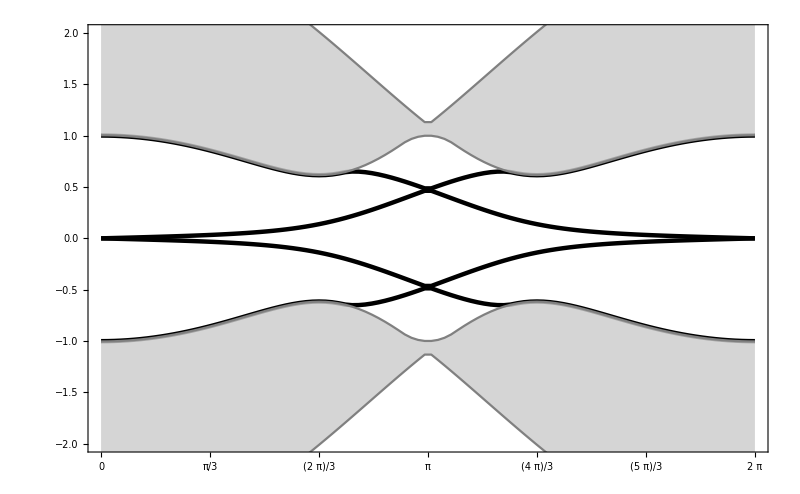

```mathematica
Show[ListPlot[ edGapless, Joined->True ,  PlotRange-> {-2,2} ,   FrameLabel->{MaTeX["q",Magnification->2] , MaTeX["\\epsilon",Magnification->2] }  ,  PlotLabel-> Style[MaTeX["\\text{Dispersion for } \\mathbf{h} = 0.85 \\, \\mathbf{c} \\text{ and } \\tilde{J} = 0.07 J  ",Magnification->2] ,20 ,Black ] ,
PlotStyle->  {{Black,Thickness[0.004]},{Black,Thickness[0.004]},{Black,Thickness[0.004]},{Black,Thickness[0.004]}},   FrameTicks->{{-π,-2π/3  , -π/3 ,0,π/3 , 2π/3  , π, 4π/3 , 5π/3  , 2π} , Automatic}   ,Joined->True,   Frame->{{True,False} ,{True,False}} , FrameStyle ->Directive[Black,26], FrameTicksStyle->Directive[Black,15],ImageSize->800],

ListPlot[ bulkGapless ,  Joined->True  ,  Filling->{2->{1}, 3-> {4}},FillingStyle->{GrayLevel[0.8,0.81]} ,PlotStyle->Gray ,Joined->True,PlotStyle->{Black},FrameStyle ->Directive[Black,26],ImageSize->800 ] ]
```

#### For J tilde greater than the critical J

```mathematica
{hx,hy,hz}=N[ 0.85{1,1,1}/Sqrt[3]];
```

```mathematica
Timing[eGapped = Energies[n,1,hx hy hz,hz, P,  0.4, -0.12740481559467198 , 0.559673459369176]]⟦1⟧/60 //Quiet
```

0.0546875

```mathematica
dGapped = dispersion[eGapped,P,n];
```

```mathematica
(*ListPlot[ dGapped , Joined->True ,  PlotRange-> All , FrameLabel->{MaTeX["q",Magnification->2] , MaTeX["\\epsilon",Magnification->2] }  ,  PlotLabel-> Style[MaTeX["\\text{Dispersion for } \\mathbf{h} = 0.85 \\, \\mathbf{c} \\text{ and } \\tilde{J} = 0.4 J ",Magnification->2] ,20 ,Black ] ,
PlotStyle->  {{Black,Thickness[0.004]},{Black,Thickness[0.004]},{Black,Thickness[0.004]},{Black,Thickness[0.004]}},   FrameTicks->{{-π,-2π/3  , -π/3 ,0,π/3 , 2π/3  , π, 4π/3 , 5π/3  , 2π} , Automatic}   ,Joined->True,   Frame->{{True,False} ,{True,False}} , FrameStyle ->Directive[Black,26], FrameTicksStyle->Directive[Black,15],ImageSize->800] *)
```

```mathematica
edGapped= edge[ dGapped,n];
bulkGapped = bulk[ dGapped,n];
```

```mathematica
Show[ListPlot[ edGapped, Joined->True ,  PlotRange-> {-2,2} ,   FrameLabel->{MaTeX["q",Magnification->2] , MaTeX["\\epsilon",Magnification->2] }  ,  PlotLabel-> Style[MaTeX["\\text{Dispersion for } \\mathbf{h} = 0.85 \\, \\mathbf{c} \\text{ and } \\tilde{J} = 0.4 J  ",Magnification->2] ,20 ,Black ] ,
PlotStyle->  {{Black,Thickness[0.004]},{Black,Thickness[0.004]},{Black,Thickness[0.004]},{Black,Thickness[0.004]}},   FrameTicks->{{-π,-2π/3  , -π/3 ,0,π/3 , 2π/3  , π, 4π/3 , 5π/3  , 2π} , Automatic}   ,Joined->True,   Frame->{{True,False} ,{True,False}} , FrameStyle ->Directive[Black,26], FrameTicksStyle->Directive[Black,15],ImageSize->600],

ListPlot[ bulkGapped ,  Joined->True  ,  Filling->{2->{1}, 3-> {4}},FillingStyle->{GrayLevel[0.8,0.81]} ,PlotStyle->Gray ,Joined->True,PlotStyle->{Black},FrameStyle ->Directive[Black,26],ImageSize->600 ] ]
```

#### Manipulate

```mathematica
(*
n = 40;
P = 50;
J = 1;
Manipulate[
eG= Energies[n,1,hx hy hz,hz, P,  bc⟦i⟧⟦1⟧, bc⟦i⟧⟦2⟧ , bc⟦i⟧⟦3⟧]//Quiet;
dG= dispersion[eG,P,n];
edG= edge[ dG,n];
bulkG = bulk[ dG,n];
title = StringForm["Dispersion for h = 0.85 c  and  J = 0 `` J",bc⟦i⟧⟦1⟧];
Show[ListPlot[ edG, Joined->True ,  PlotRange-> {-2,2} ,   FrameLabel->{MaTeX["q",Magnification->2] , MaTeX["\\epsilon",Magnification->2] }  ,  PlotLabel-> Style[MaTeX[title,Magnification->2] ,20 ,Black ],
PlotStyle->  {{Black,Thickness[0.004]},{Black,Thickness[0.004]},{Black,Thickness[0.004]},{Black,Thickness[0.004]}},   FrameTicks->{{-π,-2π/3  , -π/3 ,0,π/3 , 2π/3  , π, 4π/3 , 5π/3  , 2π} , Automatic}   ,Joined->True,   Frame->{{True,False} ,{True,False}} , FrameStyle ->Directive[Black,26], FrameTicksStyle->Directive[Black,15],ImageSize->800],

ListPlot[ bulkGapped ,  Joined->True  ,  Filling->{2->{1}, 3-> {4}},FillingStyle->{GrayLevel[0.8,0.81]} ,PlotStyle->Gray ,Joined->True,PlotStyle->{Black},FrameStyle ->Directive[Black,26],ImageSize->800 ] ]
, {i,1, Length[bc]-2}
]
*)
```

```mathematica
n = 100;
P = 200;
J = 1;
```

```mathematica
i=21+1;
eG= Energies[n,1,hx hy hz,hz, P,  bc⟦i⟧⟦1⟧, bc⟦i⟧⟦2⟧ , bc⟦i⟧⟦3⟧]//Quiet;
dG= dispersion[eG,P,n];
edG= edge[ dG,n];
bulkG = bulk[ dG,n];
title = StringForm["\\text{Dispersion for } \\mathbf{h} = 0.85 \\, \\mathbf{c} \\text{ and } \\tilde{J} = `` J",bc⟦i⟧⟦1⟧];
ListPlot[ edG, Joined->False ,  PlotRange-> {-.8,.8} ,   FrameLabel->{MaTeX["q",Magnification->2] , MaTeX["\\epsilon",Magnification->2] }  ,  PlotLabel->  Style[MaTeX[title,Magnification->2] ,20 ,Black ],
PlotStyle->  {{Black,Thickness[0.004]},{Black,Thickness[0.004]},{Black,Thickness[0.004]},{Black,Thickness[0.004]}},   FrameTicks->{{-π,-2π/3  , -π/3 ,0,π/3 , 2π/3  , π, 4π/3 , 5π/3  , 2π} , Automatic}   ,Joined->True,   Frame->{{True,False} ,{True,False}} , FrameStyle ->Directive[Black,26], FrameTicksStyle->Directive[Black,15],ImageSize->800]
```

### How the Gap scales with J̃ ?

#### sol

```mathematica
cSol= Union[{{0.,-5.998669191660753*^-14},{0.01,-0.000023146144462346553},{0.02,-0.00004751835988648067},{0.03,-0.00007408254526323681},{0.04,-0.00010394098460126548},{0.05,-0.0001384975353043768},{0.060000000000000005,-0.00017956031877135257},{0.07,-0.00022972257830976885},{0.08,-0.00029065577230992973},{0.09,-0.00036927045034124427},{0.09999999999999999,-0.0004731922345432506},{0.10999999999999999,-0.0006033084858643212},{0.11999999999999998,-0.0007932404360109966},{0.12999999999999998,-0.0010426518794959408},{0.13999999999999999,-0.0014049144970563919},{0.15,-0.0019842180343151677},{0.16,-0.0028039942228650842},{0.17,-0.004064802363130176},{0.18000000000000002,-0.005806926682324859},{0.19000000000000003,-0.008091939662849346},{0.20000000000000004,-0.010950719675347076},{0.21000000000000005,-0.014374505908245684},{0.22000000000000006,-0.018404155511166177},{0.23000000000000007,-0.022823890652217495},{0.24000000000000007,-0.02765849821987271},{0.25000000000000006,-0.03290582045555088},{0.26000000000000006,-0.03836734311724329},{0.2700000000000001,-0.04407062483334689},{0.2800000000000001,-0.050029017752459444},{0.2900000000000001,-0.05607818832222443},{0.3000000000000001,-0.06225886832196042},{0.3100000000000001,-0.06854581846055087},{0.3200000000000001,-0.07493961823474803},{0.3300000000000001,-0.08140378784164332},{0.34000000000000014,-0.08789081169409377},{0.35000000000000014,-0.09442086573038835},{0.36000000000000015,-0.10098341193220588},{0.37000000000000016,-0.10756930919037823},{0.38000000000000017,-0.11417050389513685},{0.3900000000000002,-0.12077979914715131},{0.4000000000000002,-0.12740481559467198},{0.4100000000000002,-0.13400942768591853},{0.4200000000000002,-0.14060440534978566},{0.4300000000000002,-0.14718458234521967},{0.4400000000000002,-0.1537451350552678},{0.45000000000000023,-0.1602815343480911},{0.46000000000000024,-0.1668011199774982},{0.47000000000000025,-0.17327551283367065},{0.48000000000000026,-0.1797140478972435},{0.49000000000000027,-0.18611326834169512},{0.5000000000000002,-0.19246991156815907},{0.5100000000000002,-0.19878116434716556},{0.5200000000000002,-0.20504424937318436},{0.5300000000000002,-0.2112567115500048},{0.5400000000000003,-0.2174163356400951},{0.5500000000000003,-0.22352112982182995},{0.5600000000000003,-0.2295693639268497},{0.5700000000000003,-0.23555949054553588},{0.5800000000000003,-0.24149018640784062},{0.5900000000000003,-0.2473603294633414},{0.6000000000000003,-0.253168988644746},{0.6100000000000003,-0.25891991884828364},{0.6200000000000003,-0.26460308859895987},{0.6300000000000003,-0.2702230620637436},{0.6400000000000003,-0.27577955761689543},{0.6500000000000004,-0.2812724287996291},{0.6600000000000004,-0.28670165575608936},{0.6700000000000004,-0.29206733078367747},{0.6800000000000004,-0.2973696407484801},{0.6900000000000004,-0.3026088964359929},{0.7000000000000004,-0.30778546068027307},{0.7100000000000004,-0.312899782973236},{0.7200000000000004,-0.3179523795891915},{0.7300000000000004,-0.32294382570916697},{0.7400000000000004,-0.3278747480884418},{0.7500000000000004,-0.33274581958431887},{0.7600000000000005,-0.3375577471081537},{0.7700000000000005,-0.3423112753575533},{0.7800000000000005,-0.34700717453294955},{0.7900000000000005,-0.3516462374853931},{0.8000000000000005,-0.3562292753296379},{0.8100000000000005,-0.36075711346999195},{0.8200000000000005,-0.36523058934867064},{0.8300000000000005,-0.36965054390060753},{0.8400000000000005,-0.3743028021927961},{0.8500000000000005,-0.37860097346347865},{0.8600000000000005,-0.38284933691212125},{0.8700000000000006,-0.387048656047403},{0.8800000000000006,-0.39119969650577674},{0.8900000000000006,-0.3953032240088378},{0.9000000000000006,-0.39936000254896686},{0.9100000000000006,-0.4033707927840085},{0.9200000000000006,-0.40733635062291856},{0.9300000000000006,-0.41125742598547893},{0.9400000000000006,-0.4151347617203428},{0.9500000000000006,-0.4189690926667919},{0.9600000000000006,-0.42276114484667743},{0.9700000000000006,-0.42651163477404924},{0.9800000000000006,-0.430221268870989},{0.9900000000000007,-0.43389074297907615},{1.0000000000000007,-0.43752074195680457},{1.0100000000000007,-0.4411119393541041},{1.0200000000000007,-0.4446649971558698},{1.0300000000000007,-0.4481805655871278}} , {{0.0025,-5.534883287789983*^-6},{0.0075,-0.000017383801277150865},{0.0125,-0.00002916353872136196},{0.0175,-0.00004136634140971336},{0.022500000000000003,-0.00005394499732086995},{0.027500000000000004,-0.00006712714615016538},{0.0325,-0.00008037348722207585},{0.0375,-0.00009633173803129673},{0.042499999999999996,-0.00011112851005247443},{0.047499999999999994,-0.00012912075238003},{0.05249999999999999,-0.00015009554231566042},{0.05749999999999999,-0.00017503663780438265},{0.062499999999999986,-0.00020710158646919423},{0.06749999999999999,-0.0002487680165363057},{0.0725,-0.00030711897000614734},{0.0775,-0.00047095311268635274},{0.0825,-0.0005381083378809608},{0.08750000000000001,-0.0009285486148323395},{0.09250000000000001,-0.0013270622616339477},{0.09750000000000002,-0.0018366064240797463},{0.10250000000000002,-0.0024748671207660343},{0.10750000000000003,-0.0032558944469353998},{0.11250000000000003,-0.004162692650470671},{0.11750000000000003,-0.005200463372862075},{0.12250000000000004,-0.006372913877269165},{0.12750000000000003,-0.007659160148444655},{0.13250000000000003,-0.009060739313785017},{0.13750000000000004,-0.010579600034443916},{0.14250000000000004,-0.012195874973011169},{0.14750000000000005,-0.013910740075608923},{0.15250000000000005,-0.01571982148074684},{0.15750000000000006,-0.017620797147770255},{0.16250000000000006,-0.019606928832796532},{0.16750000000000007,-0.02166953351424712},{0.17250000000000007,-0.023807524774051247},{0.17750000000000007,-0.026017132795271448},{0.18250000000000008,-0.02829438942834222},{0.18750000000000008,-0.03063543722515034},{0.1925000000000001,-0.03303656854905132},{0.1975000000000001,-0.03549580982278909}}];
```

```mathematica
bSol= Union[{{0.,-4.162971305723012*^-14},{0.01,0.004647831884441789},{0.02,0.004710839988859343},{0.03,0.004809737892123496},{0.04,0.004952437664483306},{0.05,0.005150808219058515},{0.060000000000000005,0.005421847962868142},{0.07,0.005791246345170904},{0.08,0.00628037567091825},{0.09,0.006958140329115015},{0.09999999999999999,0.007907174083053848},{0.10999999999999999,0.009157286776586891},{0.11999999999999998,0.011044702445576147},{0.12999999999999998,0.013600390634332582},{0.13999999999999999,0.01735122075475491},{0.15,0.02327367167909811},{0.16,0.031404061322200846},{0.17,0.04328119704703344},{0.18000000000000002,0.05877252298407581},{0.19000000000000003,0.07787992978693209},{0.20000000000000004,0.10028655866090619},{0.21000000000000005,0.12537914426727273},{0.22000000000000006,0.15293484395675325},{0.23000000000000007,0.18111934406299438},{0.24000000000000007,0.20987326584453417},{0.25000000000000006,0.2389725439843777},{0.26000000000000006,0.26721812267343015},{0.2700000000000001,0.2947603723890427},{0.2800000000000001,0.3216516845705917},{0.2900000000000001,0.3471804809377423},{0.3000000000000001,0.3716182050368079},{0.3100000000000001,0.3949394391745629},{0.3200000000000001,0.4172277608464468},{0.3300000000000001,0.4384255283843356},{0.34000000000000014,0.4584709853436415},{0.35000000000000014,0.47752315785760213},{0.36000000000000015,0.4956314564180262},{0.37000000000000016,0.5128469778698983},{0.38000000000000017,0.5292206714627025},{0.3900000000000002,0.5448021582900172},{0.4000000000000002,0.559673459369176},{0.4100000000000002,0.5738048361435444},{0.4200000000000002,0.5872800637275449},{0.4300000000000002,0.600138567363744},{0.4400000000000002,0.612417112369845},{0.45000000000000023,0.6241498713970991},{0.46000000000000024,0.6353907496684346},{0.47000000000000025,0.6461218533331807},{0.48000000000000026,0.6563963490877621},{0.49000000000000027,0.6662395932360523},{0.5000000000000002,0.6756750620191384},{0.5100000000000002,0.6847249342866867},{0.5200000000000002,0.6934095322117786},{0.5300000000000002,0.7017479439620438},{0.5400000000000003,0.7097580044817575},{0.5500000000000003,0.7174563844645572},{0.5600000000000003,0.7248587503984847},{0.5700000000000003,0.731979745523456},{0.5800000000000003,0.7388331404363013},{0.5900000000000003,0.7454318821246291},{0.6000000000000003,0.7517881559967322},{0.6100000000000003,0.757919075814085},{0.6200000000000003,0.763823537427677},{0.6300000000000003,0.7695181319994803},{0.6400000000000003,0.7750124958919181},{0.6500000000000004,0.7803157358151543},{0.6600000000000004,0.7854364659804596},{0.6700000000000004,0.7903828352384747},{0.6800000000000004,0.7951625483772904},{0.6900000000000004,0.7997829353917575},{0.7000000000000004,0.8042509080696512},{0.7100000000000004,0.8085730305821881},{0.7200000000000004,0.8127555280917151},{0.7300000000000004,0.8168043065392177},{0.7400000000000004,0.8207249711115414},{0.7500000000000004,0.8245228447730737},{0.7600000000000005,0.8282029788781645},{0.7700000000000005,0.8317701774672912},{0.7800000000000005,0.8352290046990077},{0.7900000000000005,0.8385838001023542},{0.8000000000000005,0.8418386911019167},{0.8100000000000005,0.8449976047923273},{0.8200000000000005,0.8480642801655964},{0.8300000000000005,0.851042273920805},{0.8400000000000005,0.8541779538407985},{0.8500000000000005,0.856971010382526},{0.8600000000000005,0.8596865081811447},{0.8700000000000006,0.8623272577608911},{0.8800000000000006,0.8648959462704625},{0.8900000000000006,0.8673951435498269},{0.9000000000000006,0.8698273078956804},{0.9100000000000006,0.8721947915381045},{0.9200000000000006,0.8744998458407897},{0.9300000000000006,0.8767446262369714},{0.9400000000000006,0.8789311969129804},{0.9500000000000006,0.8810615352510495},{0.9600000000000006,0.8831375360427073},{0.9700000000000006,0.8851610154837977},{0.9800000000000006,0.8871337149618},{0.9900000000000007,0.8890573046457928},{1.0000000000000007,0.8909333868890305},{1.0100000000000007,0.8927634994537234},{1.0200000000000007,0.894549118567233},{1.0300000000000007,0.8962916618185405}} , {{0.0025,0.004540343653949438},{0.0075,0.004649588156170319},{0.0125,0.00467178466599439},{0.0175,0.004701757734774688},{0.022500000000000003,0.0047396011389503135},{0.027500000000000004,0.004786991600217758},{0.0325,0.00483975879872428},{0.0375,0.004919751475714787},{0.042499999999999996,0.0049945457356806834},{0.047499999999999994,0.005102398560060457},{0.05249999999999999,0.005243064367066268},{0.05749999999999999,0.005427381656198724},{0.062499999999999986,0.005687882946768705},{0.06749999999999999,0.006052237314285261},{0.0725,0.0065938363149926574},{0.0775,0.008211257320915596},{0.0825,0.008848020417028526},{0.08750000000000001,0.012639386468414811},{0.09250000000000001,0.016481307971199538},{0.09750000000000002,0.021324075344277185},{0.10250000000000002,0.027244488759667455},{0.10750000000000003,0.03424372350437329},{0.11250000000000003,0.04207278968677553},{0.11750000000000003,0.0506967393298443},{0.12250000000000004,0.0600820252954468},{0.12750000000000003,0.0700241676224585},{0.13250000000000003,0.08049432626540441},{0.13750000000000004,0.09147191892899635},{0.14250000000000004,0.10279834292364451},{0.14750000000000005,0.114457431312403},{0.15250000000000005,0.1264035374924082},{0.15750000000000006,0.13860513552365816},{0.16250000000000006,0.1510066707705663},{0.16750000000000007,0.16354596853972883},{0.17250000000000007,0.1762039542599335},{0.17750000000000007,0.18894943206041845},{0.18250000000000008,0.20175093546448084},{0.18750000000000008,0.21457872471476022},{0.1925000000000001,0.2274050370692729},{0.1975000000000001,0.24021137963670822}} ];
```

/the Transpose does not work for unite this type of list, denote by bc the list of elements of the type { jt , χc , χb }

```mathematica
bc = {};
For[ i=1,i  <  Length[cSol] , i = i+1 ,  AppendTo[bc, { cSol[[i]][[1]],cSol[[i]][[2]],bSol[[i]][[2]] }] ]
```

#### calculation

```mathematica
n=200;
J=1;
{hx,hy,hz}=0.85/√3{1,1,1};
κ = hx*hy*hz;
```

```mathematica
gap = Table[ { bc⟦jt⟧⟦1⟧, Abs[Quiet@Eigenvalues[N@  HZMF[0,n,J,κ,hz,bc⟦jt⟧⟦1⟧, bc⟦jt⟧⟦2⟧,bc⟦jt⟧⟦3⟧ ] ]⟦-2⟧ ]}, {jt,1, 101 , 1}] ;
```

```mathematica
gap ;
```

```mathematica
s = OpenWrite[ "C:\\Users\\lucas\\Desktop\\lucas\\Wolfram Mathematica\\test"]
```

OutputStream[…]

```mathematica
Write[s, gap]
```

```mathematica
Close[s]
```

C:\Users\lucas\Desktop\lucas\Wolfram Mathematica\test

```mathematica
lineJc = Line[ {{0.08,0},{0.08,0.5}}] ;
```

```mathematica
Epilog-> {Directive[Thin,Black,Dashed],lineJc}
```

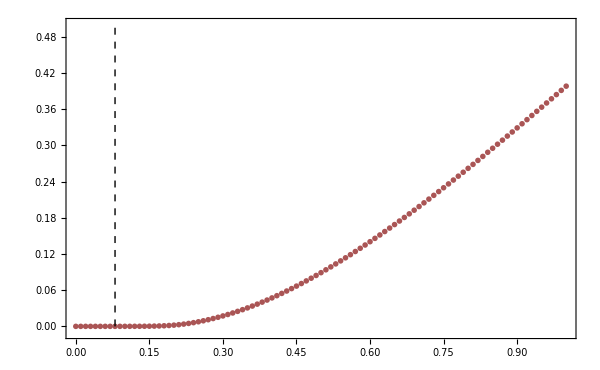

```mathematica
gp = ListPlot[ Legended[ gap ,  MaTeX["\\text{data}",Magnification->1.3] ], Joined-> False ,  PlotRange-> {-0.01,.5} ,   Epilog-> {Directive[Thin,Black,Dashed],lineJc} , FrameLabel->{MaTeX["\\tilde{J}",Magnification->2.5] , MaTeX["\\Delta_{\\gamma}",Magnification->2.5] }  ,  PlotLabel-> Style[MaTeX["\\text{Gap for the Majorana fermions at the defect}",Magnification->1.8] ,20 ,Black ] ,PlotMarkers->{"OpenMarkers",Scaled[1.1]},
PlotStyle->  Darker[Pink]   , FrameTicks->{0,.2,.4,.6,.8,1}   ,Joined->True,   Frame->True, FrameStyle ->Directive[Black,Thickness[0.0025]], FrameTicksStyle->Directive[Black,15],ImageSize->600]
```

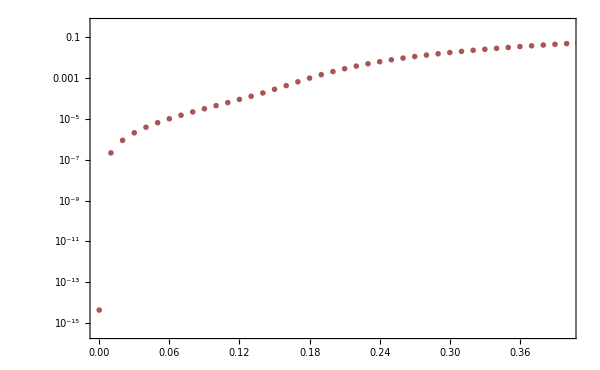

```mathematica
gLp = ListLogPlot[ Legended[ gap ,  MaTeX["\\text{data}",Magnification->1.3] ], Joined-> False ,  PlotRange->{ {0.0001,.4},Automatic} ,    Epilog-> {Directive[Thin,Black,Dashed],lineJc} ,FrameLabel->{MaTeX["\\tilde{J}",Magnification->2.5] , MaTeX["\\Delta_{\\gamma}",Magnification->2.5] }  ,  PlotLabel-> Style[MaTeX["\\text{Gap for the Majorana fermions at the defect}",Magnification->1.8] ,20 ,Black ] ,PlotMarkers->{"OpenMarkers",Scaled[1.1]},
PlotStyle->  Darker[Pink]   , FrameTicks->{0,.2,.4,.6,.8,1}   ,Joined->True,   Frame->True, FrameStyle ->Directive[Black,Thickness[0.0026]], FrameTicksStyle->Directive[Black,15],ImageSize->600]
```

#### draft -- fit function

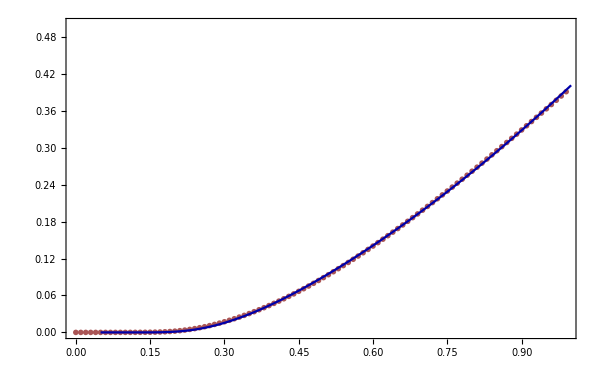

```mathematica
Show[  gp , Plot[ Legended[ g[x] , MaTeX["(0.19 x + 0.27 x^2) \\, \\text{Exp}\\left (- \\frac{ 0.15}{x^2} \\right)", Magnification->1.2] ], {x,0.05,1},  PlotRange-> {0,.5} ,  PlotStyle->  Darker[Blue] ]]
```

```mathematica
(*Show[  gp , Plot[ Legended[ g[x] , MaTeX["(a x + b x^2) \\, e^{-c/x^2}", Magnification->1.2] ], {x,0.05,1},  PlotRange-> {0,.5} ,  PlotStyle->  Darker[Blue] ]] *)
```

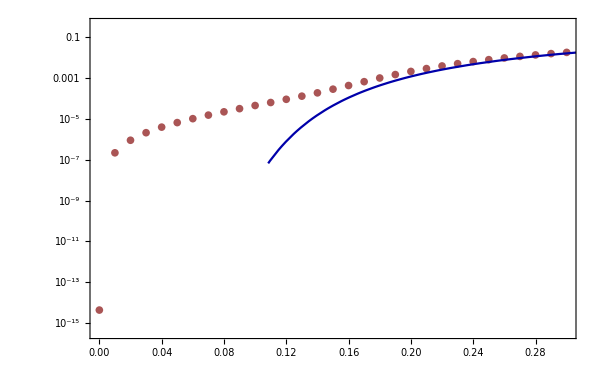

```mathematica
Show[  gLp , LogPlot[ g[x] , {x,0.015,1},  PlotRange-> {0,.5} ,  PlotStyle->  Darker[Blue] ]]
```

```mathematica
gapLog = Table[ { gap⟦i,1⟧ , Log[10 , gap⟦i,2⟧  ]}, {i , 1 , Length[ gap] } ]
```

{{0.,-14.3525},{0.01,-6.66906},{0.02,-6.05564},{0.03,-5.6867},{0.04,-5.41469},{0.05,-5.19312},{0.06,-5.00117},{0.07,-4.82723},{0.08,-4.66707},{0.09,-4.51195},{0.1,-4.3585},{0.11,-4.2116},{0.12,-4.05495},{0.13,-3.90145},{0.14,-3.73976},{0.15,-3.55985},{0.16,-3.38164},{0.17,-3.19405},{0.18,-3.01432},{0.19,-2.84673},{0.2,-2.69306},{0.21,-2.55372},{0.22,-2.4262},{0.23,-2.31342},{0.24,-2.2115},{0.25,-2.11833},{0.26,-2.03461},{0.27,-1.95803},{0.28,-1.88717},{0.29,-1.82236},{0.3,-1.76224},{0.31,-1.70622},{0.32,-1.65371},{0.33,-1.60442},{0.34,-1.55817},{0.35,-1.51447},{0.36,-1.47306},{0.37,-1.43374},{0.38,-1.39631},{0.39,-1.3606},{0.4,-1.32644},{0.41,-1.29378},{0.42,-1.26248},{0.43,-1.23242},{0.44,-1.20352},{0.45,-1.17571},{0.46,-1.14888},{0.47,-1.12303},{0.48,-1.09808},{0.49,-1.07397},{0.5,-1.05065},{0.51,-1.02808},{0.52,-1.00621},{0.53,-0.985027},{0.54,-0.964478},{0.55,-0.944536},{0.56,-0.925171},{0.57,-0.906356},{0.58,-0.888067},{0.59,-0.870277},{0.6,-0.852966},{0.61,-0.836104},{0.62,-0.819688},{0.63,-0.80369},{0.64,-0.788093},{0.65,-0.77288},{0.66,-0.758036},{0.67,-0.743545},{0.68,-0.729394},{0.69,-0.71557},{0.7,-0.702059},{0.71,-0.68885},{0.72,-0.675933},{0.73,-0.663295},{0.74,-0.650927},{0.75,-0.638819},{0.76,-0.626962},{0.77,-0.615348},{0.78,-0.603967},{0.79,-0.592813},{0.8,-0.581877},{0.81,-0.571153},{0.82,-0.560634},{0.83,-0.550312},{0.84,-0.539857},{0.85,-0.529937},{0.86,-0.520196},{0.87,-0.510628},{0.88,-0.501228},{0.89,-0.491993},{0.9,-0.482916},{0.91,-0.473994},{0.92,-0.465223},{0.93,-0.456599},{0.94,-0.448118},{0.95,-0.439776},{0.96,-0.43157},{0.97,-0.423497},{0.98,-0.415553},{0.99,-0.407736}}

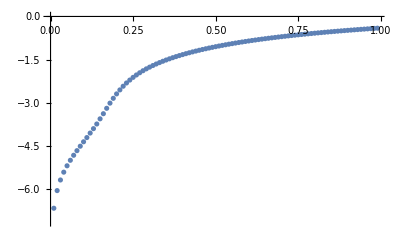

```mathematica
ListPlot[gapLog]
```

```mathematica
Fit[ gapLog ,
```

```mathematica
Clear[a,d,x]
```

```mathematica
dic = FindFit[ gap⟦2;;⟧ , { (a x^2 +e x )Exp[-d/x^2]} , {a,d,e} ,x]
```

{a→0.273067,d→0.150598,e→0.193656}

```mathematica
f[x_] =  a x^2 Exp[-d/x^2] /.  dic
```

0.433579 ⅇ^(-0.0488846/x^2) x^2

```mathematica
g[x_] = (a x^2 +e x ) Exp[-d/x^2] /.  dic
```

ⅇ^(-0.150598/x^2) (0.193656 x+0.273067 x^2)

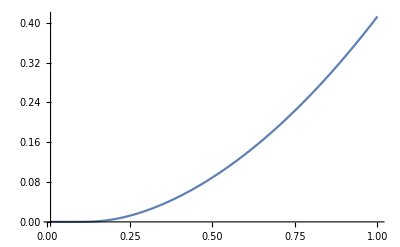

```mathematica
Plot[ f[x], {x,0.01,1}]
```

### H

```mathematica
HZMF[k,2, J,κ,h,Jt,χc,χb] //MatrixForm
```

(0 | -ⅈ h | 0 | 0 | 0 | 0 | 0 | ⅈ Jt χc
ⅈ h | 2 κ Sin[k] | -2 ⅈ J Cos[k/2] | -2 κ Sin[k/2] | 0 | 0 | ⅈ Jt χb | 0
0 | 2 ⅈ J Cos[k/2] | -2 κ Sin[k] | ⅈ J | 2 κ Sin[k/2] | 0 | 0 | 0
0 | -2 κ Sin[k/2] | -ⅈ J | 2 κ Sin[k] | -2 ⅈ J Cos[k/2] | -2 κ Sin[k/2] | 0 | 0
0 | 0 | 2 κ Sin[k/2] | 2 ⅈ J Cos[k/2] | -2 κ Sin[k] | ⅈ J | 2 κ Sin[k/2] | 0
0 | 0 | 0 | -2 κ Sin[k/2] | -ⅈ J | 2 κ Sin[k] | -2 ⅈ J Cos[k/2] | 0
0 | -ⅈ Jt χb | 0 | 0 | 2 κ Sin[k/2] | 2 ⅈ J Cos[k/2] | -2 κ Sin[k] | ⅈ h
-ⅈ Jt χc | 0 | 0 | 0 | 0 | 0 | -ⅈ h | 0)

```mathematica
H psi = E psi
```